# Ground Glass (GGX) NDF

### notation

u = m . n = Cos[θ_m]
α  = roughness

## definitions and derivations

```mathematica
GGX`D[u_,α_]:=α^2/(π (1+u^2 (-1+α^2))^2)HeavisideTheta[u]
```

```mathematica
GGX`σ[u_,α_]:=1/2(√(α^2-α^2 u^2+u^2)+u)
```

```mathematica
GGX`Λ[u_,α_]:=1/2 (-1+(√(α^2-u^2 (-1+α^2)))/u)
```

```mathematica
(1+GGX`Λ[u,α])u==GGX`σ[u,α]//FullSimplify
```

True

```mathematica
(GGX`Λ[u,α])u==GGX`σ[-u,α]//FullSimplify
```

True

```mathematica
FullSimplify[GGX`Λ[u,u/(√(1-u^2) x)],Assumptions->0<u<1&&x>0]
```

1/2 (-1+√(1+1/x^2))

### shape invariant f(x)

```mathematica
FullSimplify[GGX`D[u,α] u^4 α^2/.u->1/(√(1+x^2 α^2)),Assumptions->1-1/(√(1+x^2 α^2))>0]
```

1/(π (1+x^2)^2)

### height field normalization

```mathematica
Integrate[2Pi u GGX`D[u,α],{u,0,1},Assumptions->0<α<1]
```

1

### distribution of slopes

```mathematica
FullSimplify[GGX`D[1/(√(p^2+q^2+1)),α](1/(√(p^2+q^2+1)))^4,Assumptions->0<α<1&&p>0&&q>0]
```

α^2/(π (p^2+q^2+α^2)^2)

```mathematica
GGX`P22[p_,q_,α_]:=α^2/(π (p^2+q^2+α^2)^2)
```

```mathematica
Integrate[GGX`P22[p,q,α],{p,-Infinity,Infinity},{q,-Infinity,Infinity},Assumptions->0<α<1]
```

1

```mathematica
Integrate[GGX`P22[p,q,α],{q,-Infinity,Infinity},Assumptions->α>0&&Im[p]==0]
```

α^2/(2 (p^2+α^2)^(3/2))

```mathematica
GGX`P2[p_,α_]:=α^2/(2 (p^2+α^2)^(3/2))
```

### derivation of Λ(u)

```mathematica
FullSimplify[(√(1-u^2))/u Integrate[(q-u/(√(1-u^2)))GGX`P2[q,α],{q,u/(√(1-u^2)),Infinity},Assumptions->0<u<1&&0<α<1],Assumptions->0<u<1&&0<α<1]
```

1/2 (-1+(√(α^2-u^2 (-1+α^2)))/u)

### compare σ to delta integral:

```mathematica
Delta`σ[u_,ui_]:=Re[2(√(1-u^2-ui^2)+u ui ArcCos[-(u ui)/(√(1-u^2) √(1-ui^2))])]
```

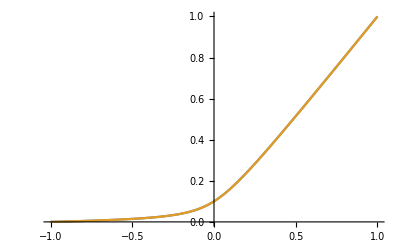

```mathematica
With[{α=.2},
Plot[{
Quiet[NIntegrate[GGX`D[ui,α]Delta`σ[u,ui],{ui,0,1}]],
GGX`σ[u,α]
},{u,-1,1}]
]
```

## As superposition of Beckmann NDFs:

### Frechet-2 superposition:

```mathematica
Beckmann`D[u_,α_]:=(ⅇ^(-(-1+1/u^2)/α^2))/(α^2 π u^4)
```

```mathematica
PDF[FrechetDistribution[2,α]][αB]
```

Piecewise[{{(2 ⅇ^(-α^2/αB^2) α^2)/αB^3, αB>0}, {0, True}}]

The GGX NDF is a Frechet-2 distribution of Beckmann NDFs:

```mathematica
FullSimplify[Integrate[(2 ⅇ^(-α^2/αB^2) α^2)/αB^3 Beckmann`D[u,αB],{αB,0,Infinity},Assumptions->α>0&&0<u<1]==GGX`D[u,α],Assumptions->0<u<1]
```

True

```mathematica
FullSimplify[Integrate[(2 ⅇ^(-1/αB^2))/αB^3 Beckmann`D[u,α αB],{αB,0,Infinity},Assumptions->α>0&&0<u<1]==GGX`D[u,α],Assumptions->0<u<1]
```

True

Which yields a new derivation of GGX Λ

```mathematica
FullSimplify[Integrate[(2 ⅇ^(-α^2/αB^2) α^2)/αB^3 Beckmann`Λ[u,αB],{αB,0,Infinity},Assumptions->α>0&&0<u<1]==GGX`Λ[u,α],Assumptions->0<u<1]
```

True

```mathematica
Integrate[(2 ⅇ^(-α^2/αB^2) α^2)/αB^3 αB,{αB,0,Infinity},Assumptions->α>0]
```

√π α

The mean squared Beckmann roughness in the superposition is unbounded:

```mathematica
Integrate[(2 ⅇ^(-α^2/αB^2) α^2)/αB^3 αB^2,{αB,0,Infinity},Assumptions->α>0]
```

Integrate[(2 ⅇ^(-α^2/αB^2) α^2)/αB,{αB,0,∞},Assumptions→α>0]

### Gamma-1 superposition

```mathematica
PDF[GammaDistribution[1,1]][αB]
```

Piecewise[{{ⅇ^-αB, αB>0}, {0, True}}]

```mathematica
FullSimplify[Integrate[ⅇ^-αB Beckmann`D[u,α/√αB],{αB,0,Infinity},Assumptions->α>0&&0<u<1]==GGX`D[u,α],Assumptions->0<u<1]
```

True

```mathematica
FullSimplify[Integrate[ⅇ^-αB Beckmann`Λ[u,α/√αB],{αB,0,Infinity},Assumptions->α>0&&0<u<1]==GGX`Λ[u,α],Assumptions->0<u<1]
```

True